# Paper 1 -Random Energy Model

Copy of code from *QGates**_D1018.nb that is required to get the plots.
===================
Run1:
T = 10^6, 10^4, 10^2, 1, 10^-2, 10^-4, 10^-6, 10^-8
Range = 50, 10, 5, 1 , 0.5, 0.1, 0.05, 0.01
Ns=4
Ne=12, 20
gs=4
ge=1,8,16

===================
Run2:
T = 10^4, 10^2, 1, 10^-2, 10^-4, 10^-6, 10^-8
Range =2
Ns=4
Ne=4,8,12,16,20
gs=4
gp=1,4,8,12,16

===================
Run3:
T = 10^4, 10^2, 1, 10^-2, 10^-4, 10^-6, 10^-8
Range =2
Ns=4
Ne=18
gs=4
gp1=1,4,8
gp2=1,4,8
gp3=1,4,8
gsGap=0.1,0.01,0.001,0.0001,0.00001,
higherGap=0.5

```mathematica
multipleDegenerateList[8,{2,2},0.1,0.5,{-2,2}]
```

multipleDegenerateList[8,{2,2},0.1,0.5,{-2,2}]

```mathematica
(* creates a list of length Len of random number within range and with degeneracy of degen*)
createDegenerateList[len_Integer,degen_Integer,range:{min_?NumericQ,max_?NumericQ}:{-1,1}]/;1<=degen<=len&&min<max:=With[{baseNumbers=Sort[RandomReal[range,len-degen+1]]},Join[Table[First[baseNumbers],degen],Rest[baseNumbers]]]

(* 
creates a list of length Len of random number within range and with multiple degeneracies of degen.
gsGAp is gap between degeneracies
higherGap is gap between the highest of the degeneracies and the next higher energy level
0 and 1 are same degeneracies but 1 ensure that gsGap and higherGap is maintained.
*)
multipleDegenerateList[
len_Integer,
degeneracies:{__Integer?NonNegative},
gsGap_?NumericQ,
higherGap_?NumericQ,
range:{min_?NumericQ,max_?NumericQ}:{-1,1}
]:=Module[
{
initialList,gs,numDegenerate,numHigher,degeneratePart,lastDegenerateValue,lowerBound,upperBound,higherPart},

(*1. Sum degeneracies*)
numDegenerate=Total[degeneracies];

(*2. Create initial random list*)
initialList=RandomReal[range,len];

(*Check if degeneracies list was empty.If so,return the initial list.*)
If[numDegenerate==0,
Sort[initialList],
(*ELSE:Proceed with the original logic*)

(*3. Find ground state*)
gs=Min[initialList];

(*4. Create degenerate part*)
degeneratePart=Flatten[
Table[gs+(k-1)*gsGap,
{k,1,Length[degeneracies]},
{degeneracies[[k]]}
]
];
(*Calculate how many higher elements are needed*)
numHigher=len-numDegenerate;
(*Check if degenerate part is already too long*)
If[numHigher<=0,
(*If so,return only the first'len' elements of the degenerate part*)
Take[degeneratePart,len],

(*5. Create rest of the elements*)
(*Find the value of the last degenerate level.*)
(*This block is now guaranteed to have Length[degeneracies]>=1*)
lastDegenerateValue=gs+(Length[degeneracies]-1)*gsGap;
(*Define the range for the higher elements*)
lowerBound=lastDegenerateValue+higherGap;
upperBound=range[[2]];(*This is'max'*)
(*Generate the higher part,handling invalid ranges*)
higherPart=If[lowerBound>=upperBound,
(*If gap pushes past max,fill with the lower bound*)
Table[lowerBound,{numHigher}],
(*Otherwise,generate randoms in the valid range*)
Sort[RandomReal[{lowerBound,upperBound},numHigher]]
];
(*Print["last GS: ",lastDegenerateValue," Lower bound: ",lowerBound," Higher Part: ",higherPart];*)
(*Join the parts to form the final list*)
Join[degeneratePart,higherPart]
]
]
]


randomState[n_Integer]:=Module[{nState,r0,r1,wf},
nState=2^n;
r0=RandomReal[{0,1},nState];
r1=RandomReal[{0,1},nState];
wf=Sqrt[-2 Log[r0]] Cos[2 Pi r1]+I Sqrt[-2 Log[r0]] Sin[2 Pi r1];
wf/Norm[wf]
]

(*Calculates canonical thermal state in eigen basis.This is to reduce numerical instability*)
eigenCanonicalState[eVal_,wavefun_,T_]:=Module[{result},
(*Apply exp(-eigenvalue/(2*T)) to each component*)
result=Exp[-eVal/(2*T)]*wavefun;

(*Normalize the result*)
result/Norm[result]
]

(*calculate the complete H (Hamiltonian) given subsystem (system and environment) H*)
mergeEs[sys_,env_]:=Module[{nSys,nEnv, Htotal},
nSys=Length[sys];
nEnv = Length[env];
Htotal = Flatten[KroneckerProduct[ConstantArray[1,nEnv],sys]]+Flatten[KroneckerProduct[env, ConstantArray[1,nSys]]]
]

(*Calculates the reduced density Matrix of the system.*)
reducedDensityMatrix[psi_,dims_]:=Module[{sysQubits,envQubits,sysDim,envDim,psiMatrix},
sysQubits=dims[[1]];
envQubits=dims[[2]];
sysDim=2^sysQubits;
envDim=2^envQubits;
(*Reshape the state vector into a matrix*)
psiMatrix=ArrayReshape[psi,{envDim,sysDim}];
(*Compute reduced density matrix as psiMatrix†.psiMatrix*)
Transpose[psiMatrix].Conjugate[ psiMatrix]
]

(*Calculate Thermalization*)
thermalization[ρ_,E_,dims_,ignoreE_:1`512*10^-6]:=Module[{sysQubits,sysDim,bNum,bDen,realE,,bcalc, b,Esum,delsqr,sqrtDelsqr},
sysQubits=dims[[1]];
sysDim=2^sysQubits;
bNum=0;
bDen=0;
realE=Re[E];

Do[
Do[
If[Abs[realE[[i]]-realE[[j]]]>ignoreE && (Abs[ρ[[i,i]]]>1000*ignoreE || Abs[ρ[[j,j]]]>1000*ignoreE),
(*bcalc = (Log[Re[ρ[[i,i]]]]-Log[Re[ρ[[j,j]]]+$MachineEpsilon])/(realE[[j]]-realE[[i]]);*)
bcalc=(Log[Re[ρ[[i,i]]]]-If[Re[ρ[[j,j]]]==0,Log[$MachineEpsilon],Log[Re[ρ[[j,j]]]]])/(realE[[j]]-realE[[i]]);
bNum+= bcalc;
bDen+=1;
(*Print["i = ", i, " j = ", j, " ρ[[i,i]] = ", ρ[[i,i]], " ρ[[j,j]] = ", ρ[[j,j]],  "       b =",bcalc," bNum = ", bNum , "  bDen = ", bDen];*)
],
{j,i+1,sysDim}
],
{i,1,sysDim-1}
];

b=Re[bNum/bDen];
Esum=Sum[Exp[-b*realE[[i]]],{i,1,sysDim}];
delsqr=Sum[(Re[ρ[[i,i]]]-Exp[-b*realE[[i]]]/Esum)^2,{i,1,sysDim}];
sqrtDelsqr=Sqrt[delsqr];
{sqrtDelsqr,b}
]

(*Thermalization based on degenerate ground states*)
gsThermalization[ρ_,E_,dims_, gs_]:=Module[{sysQubits,sysDim,bNum,bDen,realE,b,Esum,delsqr,sqrtDelsqr,nextStateIndex,degenerateEnergy,nextEnergy,bList},
sysQubits=dims[[1]];
sysDim=2^sysQubits;
bNum=0;
bDen=0;
realE=Re[E];
nextStateIndex=gs+1;

degenerateEnergy=realE[[1]];
nextEnergy=realE[[nextStateIndex]];
(*bList=Table[(Log[Re[ρ[[i,i]]]]-Log[Re[ρ[[nextStateIndex,nextStateIndex]]]+$MachineEpsilon])/(nextEnergy-degenerateEnergy),{i,1,gs}];*)
bList=Table[(Log[Re[ρ[[i,i]]]]-If[Re[ρ[[nextStateIndex,nextStateIndex]]]==0,Log[$MachineEpsilon],Log[Re[ρ[[nextStateIndex,nextStateIndex]]]]])/(nextEnergy-degenerateEnergy),{i,1,gs}];
b=Mean[bList];
Esum=Sum[Exp[-b*realE[[i]]],{i,1,sysDim}];
delsqr=Sum[(Re[ρ[[i,i]]]-Exp[-b*realE[[i]]]/Esum)^2,{i,1,sysDim}];
sqrtDelsqr=Sqrt[delsqr];
{sqrtDelsqr,b}
]

(*Thermalization based on predefined temperature*)
PreTThermalization[ρ_,E_,dims_,T_]:=Module[{sysQubits,sysDim,bNum,bDen,realE,b,Esum,delsqr,sqrtDelsqr},
sysQubits=dims[[1]];
sysDim=2^sysQubits;
bNum=0;
bDen=0;
realE=Re[E];

b=1/T;
Esum=Sum[Exp[-b*realE[[i]]],{i,1,sysDim}];
delsqr=Sum[(Re[ρ[[i,i]]]-Exp[-b*realE[[i]]]/Esum)^2,{i,1,sysDim}];
sqrtDelsqr=Sqrt[delsqr];
{sqrtDelsqr,b}
]
```

```mathematica
(*Calculate Partition Function*)
z[energy_,beta_]:=Sum[Exp[-beta*e],{e,energy}]

(*Calculate free energy from equation 24*)
F[energy_, beta_] := -Log[z[energy,beta]]/beta

(*Thermalization at Infinite temperature from system and environment dimensions based on calculation on equation B77*)
calculatedThermalizationInfTemp[dims_]:=Module[{sysQubits,envQubits,sysDim,envDim,totDim, sigma},
(* Based on equation B77 on 2016 paper*)
sysQubits=dims[[1]];
envQubits=dims[[2]];
sysDim=2^sysQubits;
envDim=2^envQubits;
totDim = 2^(sysQubits+envQubits);
sigma = Sqrt[(sysDim-1)/(sysDim*(totDim+1))]
] 

(*Thermalization at zero temperature based on calculation on equation B80*)
calculatedThermalizationZeroTemp[dims_, gs_, gb_]:=Module[{sysQubits,envQubits,sysDim,envDim,totDim, sigma},
(* Based on equation B77 on 2016 paper*)
sysQubits=dims[[1]];
envQubits=dims[[2]];
sysDim=2^sysQubits;
envDim=2^envQubits;
totDim = 2^(sysQubits+envQubits);
sigma = Sqrt[(gs-1)*totDim/(gs*gs*gb*(totDim+1))]
] 

(*Decoherence at Infinite temperature from system and environment dimensions based on calculation on equation 28*)
calculatedDecoherenceInfTemp[dims_]:=Module[{sysQubits,envQubits,sysDim,envDim,totDim, sigma},
(* Based on equation B129 on 2016 paper*)
sysQubits=dims[[1]];
envQubits=dims[[2]];
sysDim=2^sysQubits;
envDim=2^envQubits;
totDim = 2^(sysQubits+envQubits);
sigma = Sqrt[(sysDim-1)/(2(totDim+1))]
] 

(*Decoherence at zero temperature from system dimensions and degeneracy based on calculation on equation 28*)
calculatedDecoherenceZeroTemp[dims_, gs_, gb_]:=Module[{sysQubits,envQubits,sysDim,envDim,totDim, sigma},
(* Based on equation B129 on 2016 paper*)
sysQubits=dims[[1]];
envQubits=dims[[2]];
sysDim=2^sysQubits;
envDim=2^envQubits;
totDim = 2^(sysQubits+envQubits);
sigma = Sqrt[(gs-1)*(1-(sysDim*envDim/(gs*gb*(sysDim*envDim+1))))/(2*gs*gb)]
] 

(*calculate thermalization from Eigenvalues and partition function from Equation B76*)
calcThermalizationFromPartition[Esys_,Eenv_, beta_]:=Module[{Ds,De,D, deltaSqr},
Ds = Length[Esys];
De  = Length[Eenv];
D = Ds * De;
deltaSqr = (D/(D+1)) * (z[Eenv,2*beta]/(z[Eenv, beta])^2) * ( z[Esys,2*beta]/(z[Esys, beta])^2 - 2*z[Esys,3*beta]/(z[Esys, beta])^3 + (z[Esys,2*beta])^2/(z[Esys, beta])^4 );
Sqrt[deltaSqr]
]

(*Calculate decoherence from Eigenvalues and partition function based on calculation on equation 22*)
calcDecoherenceFromPartition[Esys_,Eenv_, beta_]:=Module[{Ds,De,D, sigmaSqr},
Ds = Length[Esys];
De  = Length[Eenv];
D = Ds * De;
sigmaSqr = z[Eenv,2*beta]/(2*z[Eenv, beta]^2) * ( 1- (z[Esys,2*beta]/z[Esys, beta]^2))-(2*D*z[Eenv,3*beta]/((D+1)*z[Eenv, beta]^3))*((z[Esys,2*beta]/z[Esys, beta]^2)-(z[Esys,3*beta]/z[Esys, beta]^3))+(3*D*z[Esys,2*beta]*z[Eenv,2*beta]^2/(2*(D+1)*z[Esys, beta]^2*z[Eenv, beta]^4))*( 1- (z[Esys,2*beta]/z[Esys, beta]^2));
Sqrt[sigmaSqr]
]

simulatedDecoherence[ρ_,dims_]:=Module[{sysQubits,sysDim,σSqr,σ},
sysQubits=dims[[1]];
sysDim=2^sysQubits;
σSqr=0;
Do[
Do[

σSqr+=Abs[ρ[[i,j]]]^2;
(*Print["i = ", i, " j = ", j,"    Abs = ",Abs[ρ[[i,j]]]^2," σSqr = ", σSqr]*),
{j,i+1,sysDim}
],
{i,1,sysDim-1}
];

σ=Sqrt[σSqr];
σ
]
```

```mathematica
(*Function to create heatmap for complex matrices with options for magnitude or phase*)
Options[LabeledComplexHeatmap]={DisplayMode->"Magnitude", ImageSize->800, ShowLegend->True};

LabeledComplexHeatmap[matrix_,OptionsPattern[]]:=Module[{data,labels,rows,cols,inputMatrix, imageSize, showLegend},
(*Ensure the input is treated as a matrix*)
inputMatrix=If[MatrixQ[matrix],matrix,{matrix}];

(*Extract user-specified ImageSize or use default*)
imageSize=OptionValue[ImageSize];
showLegend=OptionValue[ShowLegend];

(*Select data to plot based on user choice*)
data=Switch[
OptionValue[DisplayMode],
"Magnitude",Abs[inputMatrix],
"Phase",Arg[inputMatrix],
_,
Abs[inputMatrix] (*Default to magnitude if not specified*)
];

(*Generate labels based on display mode*)
labels=Table[
If[OptionValue[DisplayMode]=="Magnitude",
NumberForm[Abs[inputMatrix[[i,j]]],{3,2}],
NumberForm[Arg[inputMatrix[[i,j]]],{3,2}]
],
{i,Length[inputMatrix]},{j,Length[inputMatrix[[1]]]}
];

(*Dimensions of the input matrix*)
{rows,cols}=Dimensions[inputMatrix];

(*Plot the heatmap with labels*)
MatrixPlot[
data,
ColorFunction->"ThermometerColors",
Frame->True,
PlotLegends->If[showLegend,Automatic,None],
Mesh->True,
ImageSize->imageSize,
Epilog->Table[
Text[
Style[labels[[i,j]],Black,Bold],{j-0.5,rows-i+0.5}],
{i,rows},{j,cols}
]
]
]


(*Example usage with a complex matrix*)
(*complexMatrix=RandomComplex[{0+0 I,1+1 I},{5,5}];
LabeledComplexHeatmap[complexMatrix,DisplayMode->"Magnitude"] (*For magnitudes*)
LabeledComplexHeatmap[complexMatrix,DisplayMode->"Phase"]     (*For phases*)*)
```

```mathematica
(*Base code from*QGates**_D1018.nb*)

dims = {4,5};

SeedRandom[1234];
gs=4;
ge=16
es=createDegenerateList[2^dims[[1]],gs,{-2,2}];
ee=createDegenerateList[2^dims[[2]],ge,{-2,2}];
et = mergeEs[es,ee];

Temp = 0.000001;

calcSigmaInf = N[calculatedDecoherenceInfTemp[dims]];
calcDeltaInf = N[calculatedThermalizationInfTemp[dims]];
calcDeltaZer = N[calculatedThermalizationZeroTemp[dims,gs,ge]]
calcSigmaZer = N[calculatedDecoherenceZeroTemp[dims,gs,ge]]
calcDeltaPar = N[calcThermalizationFromPartition[es,ee,1/Temp]]
calcSigmaPar = N[calcDecoherenceFromPartition[es,ee,1/Temp]]

numTrials = 1;
Print[dims];
dTotSum = ConstantArray[0,{2^(dims[[1]]),2^(dims[[1]])}];
sigmaSeries={};
deltaSeries = {};
betaSeries = {};
deltaSeries1 = {};
betaSeries1 = {};
deltaSeries2 = {};
betaSeries2 = {};

For[trial=1,trial<=numTrials,trial=trial+1,
psi = randomState[dims[[1]]+dims[[2]]];
psiTotCan =N[eigenCanonicalState[et,psi, Temp]];
dTot = N[reducedDensityMatrix[psiTotCan, dims]];
dTotSum = dTotSum + dTot;
{delta,beta}=N[thermalization[dTot,es,dims]];
{delta1,beta1}=N[gsThermalization[dTot,es,dims,gs]];
{delta2,beta2}=N[PreTThermalization[dTot,es,dims, Temp]];
sigma = N[simulatedDecoherence[dTot,dims]];
AppendTo[sigmaSeries,sigma];
AppendTo[deltaSeries,delta];
AppendTo[betaSeries,beta];
AppendTo[deltaSeries1,delta1];
AppendTo[betaSeries1,beta1];
AppendTo[deltaSeries2,delta2];
AppendTo[betaSeries2,beta2];

(*Print[LabeledComplexHeatmap[psiTotCan,DisplayMode->"Magnitude", ImageSize -> 1600, ShowLegend->False]]; *)
(*
Print[ "T = ", Temp, " Trial: ", trial, ";       Beta: ", NumberForm[beta,{9,8}], ";       Beta1: ", NumberForm[beta1,{9,8}], ";       Beta2: ", NumberForm[beta2,{9,8}], "   Delta: ", NumberForm[delta,{9,8}], ";   Delta2: ", NumberForm[delta2,{9,8}], ";   Calc Inf T delta: ", NumberForm[calcDeltaInf,{9,8}], ";   Calc Zero T delta: ", NumberForm[calcDeltaZer,{9,8}], ";    Calc Part delta: ", NumberForm[calcDeltaPar,{9,8}]];
*)

(*Print[LabeledComplexHeatmap[psiTotCan,DisplayMode->"Phase", ImageSize -> 1600, ShowLegend->False]]; *)
(*
Print[ "T = ", Temp, " Trial: ", trial, ";       Sigma: ", NumberForm[sigma,{9,8}], ";   Calc Inf T Sigma: ", NumberForm[calcSigmaInf,{9,8}], ";   Calc Zero T Sigma: ", NumberForm[calcSigmaZer,{9,8}], ";     Calc Part Sigma: ", NumberForm[calcSigmaPar,{9,8}]];
*)

];

Print["Magnitude plot below at T = ",Temp];
Print[LabeledComplexHeatmap[dTot,DisplayMode->"Magnitude", ImageSize->400]]; 
Print["Phase plot below at T = ",Temp];
Print[LabeledComplexHeatmap[dTot,DisplayMode->"Phase", ImageSize->400]];
Print["Summed Magnitude plot below at T = ",Temp, "   Beta: ", NumberForm[Mean[betaSeries],{9,8}], "   Beta1: ", NumberForm[Mean[betaSeries1],{9,8}], "   Beta2: ", NumberForm[Mean[betaSeries2],{9,8}], "   Delta: ", NumberForm[Mean[deltaSeries],{9,8}], "   Delt1: ", NumberForm[Mean[deltaSeries1],{9,8}], "   Delta2: ", NumberForm[Mean[deltaSeries2],{9,8}], "   Calc Part delta: ",NumberForm[calcDeltaPar,{9,8}] ];
Print[LabeledComplexHeatmap[dTotSum/numTrials,DisplayMode->"Magnitude", ImageSize->400]]; 
Print["Summed Phase plot below at T = ",Temp,"   Sigma: ", NumberForm[Mean[sigmaSeries],{9,8}],"   Calc Part Sigma: ", NumberForm[calcSigmaPar,{9,8}]];
Print[LabeledComplexHeatmap[dTotSum/numTrials,DisplayMode->"Phase", ImageSize->400]];
```

16

0.108148

0.151895

General::munfl: Exp[-670834.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-703541.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.06193×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.108148

General::munfl: Exp[-670834.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-703541.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.06193×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.151895

{4,5}

General::munfl: 2.86013924912066×10^-64780-4.7179358640854×10^-64780 ⅈ is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.61472225678192×10^-178411-1.78494538241914×10^-178410 ⅈ is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.38063997219246×10^-202996-2.72437399282729×10^-202995 ⅈ is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Magnitude plot below at T = 1.×10^-6

-Graphics-

Phase plot below at T = 1.×10^-6

-Graphics-

Summed Magnitude plot below at T = 1.×10^-6   Beta: 27.50111480   Beta1: 116.10974200   Beta2: 1.00000000×10^6   Delta: 0.10443379   Delt1: 0.10443376   Delta2: 0.10443376   Calc Part delta: 0.10814761

-Graphics-

Summed Phase plot below at T = 1.×10^-6   Sigma: 0.11690236   Calc Part Sigma: 0.15189471

-Graphics-

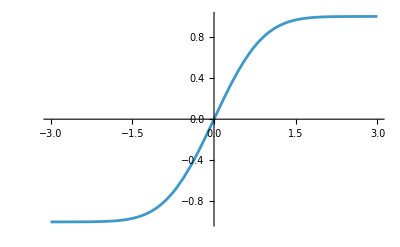

```mathematica
Plot[Erf[x],{x,-3,3}]
```

```mathematica
(*
10/21, Update to set es at the beginning so as to keep it same across runs, moved the seed inside the loop
Run1 for following ranges
T=10^6,10^4,10^2,1,10^-2,10^-4,10^-6,10^-8
Range=50,10,5,1,0.5,0.1,0.05,0.01
Ns=4
Ne=12,20
gs=4
ge=1,8,16
*)



Temperature = {10^2,10, 1,10^-1, 10^-2,10^-3, 10^-4,10^-5,10^-6,10^-8, 10^-9};
HighLow={10,1,0.1,0.01};
Nes = {20};
ges = {8};
numTrials = 100;

(*---File Initialization---*)
(*Create and open the file for individual trial data,then write the header row*)
timeStamp=DateString[{"Year","Month","Day","-","Hour","Minute","Second"}];
Paper1Run1DataFile="paper1_run1_data_"<>timeStamp<>".csv";
P1R1Stream=OpenWrite[Paper1Run1DataFile];
WriteString[P1R1Stream,"Temperature,Range,Ne,Ns,gs,ge,Trial, sigma,delta,beta,delta1,beta1,delta2,beta2,calcDeltaInf,calcSigmaInf,calcDeltaZer,calcSigmaZer,calcDeltaPar,calcSigmaPar\n"];

SeedRandom[1234];
Ns=4;
gs=4;
es=createDegenerateList[2^Ns,gs,{-1,1}];
For[Ri=1,Ri<=Length[HighLow],Ri++,
SeedRandom[1234+Ri];
R = HighLow[[Ri]];
For[Ti=1,Ti<=Length[Temperature],Ti++,
Temp = Temperature[[Ti]];
For[Nei=1,Nei<=Length[Nes],Nei++,
Ne=Nes[[Nei]];
dims = {Ns,Ne};
For[gei=1,gei<=Length[ges],gei++,
ge=ges[[gei]];
SeedRandom[1234+Ri+10*Ti];
ee=createDegenerateList[2^dims[[2]],ge,{-R,R}];
et = mergeEs[es,ee];

calcSigmaInf = N[calculatedDecoherenceInfTemp[dims]];
calcDeltaInf = N[calculatedThermalizationInfTemp[dims]];
calcDeltaZer = N[calculatedThermalizationZeroTemp[dims,gs,ge]];
calcSigmaZer = N[calculatedDecoherenceZeroTemp[dims,gs,ge]];
calcDeltaPar = N[calcThermalizationFromPartition[es,ee,1/Temp]];
calcSigmaPar = N[calcDecoherenceFromPartition[es,ee,1/Temp]];

Print[dims];
dTotSum = ConstantArray[0,{2^(dims[[1]]),2^(dims[[1]])}];
sigmaSeries={};
deltaSeries = {};
betaSeries = {};
deltaSeries1 = {};
betaSeries1 = {};
deltaSeries2 = {};
betaSeries2 = {};

For[trial=1,trial<=numTrials,trial=trial+1,
psi = randomState[dims[[1]]+dims[[2]]];
psiTotCan =N[eigenCanonicalState[et,psi, Temp]];
dTot = N[reducedDensityMatrix[psiTotCan, dims]];
dTotSum = dTotSum + dTot;
{delta,beta}=N[thermalization[dTot,es,dims]];
{delta1,beta1}=N[gsThermalization[dTot,es,dims,gs]];
{delta2,beta2}=N[PreTThermalization[dTot,es,dims, Temp]];
sigma = N[simulatedDecoherence[dTot,dims]];
AppendTo[sigmaSeries,sigma];
AppendTo[deltaSeries,delta];
AppendTo[betaSeries,beta];
AppendTo[deltaSeries1,delta1];
AppendTo[betaSeries1,beta1];
AppendTo[deltaSeries2,delta2];
AppendTo[betaSeries2,beta2];

(*---Write Trial Data to CSV---*)(*Create a comma-separated string for the current trial's data*)rowString=StringRiffle[{Temp,R,Ne,Ns,gs,ge,trial, sigma,delta,beta,delta1,beta1,delta2,beta2,calcDeltaInf,calcSigmaInf,calcDeltaZer,calcSigmaZer,calcDeltaPar,calcSigmaPar},","];
(*Write the string as a new line in the trial data file*)
WriteString[P1R1Stream,rowString,"\n"];

];

Print["Summed Magnitude plot below at T = ",Temp, "   Beta: ", NumberForm[Mean[betaSeries],{9,8}], "   Beta1: ", NumberForm[Mean[betaSeries1],{9,8}], "   Beta2: ", NumberForm[Mean[betaSeries2],{9,8}], "   Delta: ", NumberForm[Mean[deltaSeries],{9,8}], "   Delt1: ", NumberForm[Mean[deltaSeries1],{9,8}], "   Delta2: ", NumberForm[Mean[deltaSeries2],{9,8}], "   Calc Part delta: ",NumberForm[calcDeltaPar,{9,8}],"   Sigma: ", NumberForm[Mean[sigmaSeries],{9,8}],"   Calc Part Sigma: ", NumberForm[calcSigmaPar,{9,8}] ];
Print[LabeledComplexHeatmap[dTotSum/numTrials,DisplayMode->"Magnitude", ImageSize->400]]; 
];
];
];
];

Close[Paper1Run1DataFile];
```

{4,20}

Summed Magnitude plot below at T = 100   Beta: 0.00997074   Beta1: 0.01095557   Beta2: 0.01000000   Delta: 0.00023501   Delt1: 0.00100256   Delta2: 0.00022889   Calc Part delta: 0.00023679   Sigma: 0.00067176   Calc Part Sigma: 0.00066972

-Graphics-

{4,20}

Summed Magnitude plot below at T = 10   Beta: 0.10016561   Beta1: 0.09995741   Beta2: 0.10000000   Delta: 0.00026765   Delt1: 0.00108886   Delta2: 0.00026590   Calc Part delta: 0.00027135   Sigma: 0.00076216   Calc Part Sigma: 0.00076605

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1   Beta: 0.99998889   Beta1: 1.00061508   Beta2: 1.00000000   Delta: 0.00086586   Delt1: 0.00233424   Delta2: 0.00085764   Calc Part delta: 0.00084194   Sigma: 0.00208054   Calc Part Sigma: 0.00209420

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/10   Beta: 10.00069470   Beta1: 10.00393420   Beta2: 10.00000000   Delta: 0.00362760   Delt1: 0.00356960   Delta2: 0.00363315   Calc Part delta: 0.00402247   Sigma: 0.00593594   Calc Part Sigma: 0.00607768

-Graphics-

General::munfl: Exp[-708.397] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-708.402] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-708.408] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{4,20}

Summed Magnitude plot below at T = 1/100   Beta: 99.99761710   Beta1: 100.00233300   Beta2: 100.00000000   Delta: 0.01260552   Delt1: 0.01260552   Delta2: 0.01260552   Calc Part delta: 0.01311057   Sigma: 0.01844503   Calc Part Sigma: 0.01853631

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/1000   Beta: 351.84613900   Beta1: 999.95907600   Beta2: 1000.00000000   Delta: 0.03624994   Delt1: 0.03624994   Delta2: 0.03624994   Calc Part delta: 0.04224339   Sigma: 0.05709538   Calc Part Sigma: 0.05959022

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/10000   Beta: 55.00396100   Beta1: 232.22679400   Beta2: 10000.00000000   Delta: 0.08870367   Delt1: 0.08870363   Delta2: 0.08870363   Calc Part delta: 0.09917893   Sigma: 0.13551867   Calc Part Sigma: 0.13885290

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/100000   Beta: 54.95369240   Beta1: 232.01456000   Beta2: 100000.00000000   Delta: 0.14203424   Delt1: 0.14203422   Delta2: 0.14203422   Calc Part delta: 0.15305609   Sigma: 0.20829458   Calc Part Sigma: 0.21304342

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/1000000   Beta: 54.96163730   Beta1: 232.04810400   Beta2: 1.00000000×10^6   Delta: 0.13258523   Delt1: 0.13258520   Delta2: 0.13258520   Calc Part delta: 0.15309267   Sigma: 0.20863777   Calc Part Sigma: 0.21309597

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/100000000   Beta: 54.95547200   Beta1: 232.02207400   Beta2: 1.00000000×10^8   Delta: 0.13736185   Delt1: 0.13736182   Delta2: 0.13736182   Calc Part delta: 0.15309310   Sigma: 0.20215385   Calc Part Sigma: 0.21309659

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/1000000000   Beta: 54.95480800   Beta1: 232.01927000   Beta2: 1.00000000×10^9   Delta: 0.14536412   Delt1: 0.14536410   Delta2: 0.14536410   Calc Part delta: 0.15309311   Sigma: 0.20196255   Calc Part Sigma: 0.21309659

-Graphics-

{4,20}

Summed Magnitude plot below at T = 100   Beta: 0.00995623   Beta1: 0.00957692   Beta2: 0.01000000   Delta: 0.00023636   Delt1: 0.00102203   Delta2: 0.00022948   Calc Part delta: 0.00023640   Sigma: 0.00066735   Calc Part Sigma: 0.00066862

-Graphics-

{4,20}

Summed Magnitude plot below at T = 10   Beta: 0.10012961   Beta1: 0.09991137   Beta2: 0.10000000   Delta: 0.00023234   Delt1: 0.00098152   Delta2: 0.00022980   Calc Part delta: 0.00023719   Sigma: 0.00067166   Calc Part Sigma: 0.00066962

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1   Beta: 1.00002552   Beta1: 1.00083502   Beta2: 1.00000000   Delta: 0.00030090   Delt1: 0.00089136   Delta2: 0.00030175   Calc Part delta: 0.00030457   Sigma: 0.00075288   Calc Part Sigma: 0.00075757

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/10   Beta: 9.99962727   Beta1: 10.00235360   Beta2: 10.00000000   Delta: 0.00123314   Delt1: 0.00121226   Delta2: 0.00123447   Calc Part delta: 0.00127126   Sigma: 0.00191079   Calc Part Sigma: 0.00192083

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/100   Beta: 100.00206500   Beta1: 100.01174800   Beta2: 100.00000000   Delta: 0.00400902   Delt1: 0.00400902   Delta2: 0.00400902   Calc Part delta: 0.00424619   Sigma: 0.00578215   Calc Part Sigma: 0.00600485

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/1000   Beta: 272.46132600   Beta1: 999.99359000   Beta2: 1000.00000000   Delta: 0.01275819   Delt1: 0.01275819   Delta2: 0.01275819   Calc Part delta: 0.01335376   Sigma: 0.01838690   Calc Part Sigma: 0.01887993

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/10000   Beta: 55.02919440   Beta1: 232.33333000   Beta2: 10000.00000000   Delta: 0.03674559   Delt1: 0.03674549   Delta2: 0.03674549   Calc Part delta: 0.04250012   Sigma: 0.05699802   Calc Part Sigma: 0.05993559

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/100000   Beta: 55.00074480   Beta1: 232.21321600   Beta2: 100000.00000000   Delta: 0.09457072   Delt1: 0.09457069   Delta2: 0.09457069   Calc Part delta: 0.09912429   Sigma: 0.13508645   Calc Part Sigma: 0.13865923

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/1000000   Beta: 54.96695270   Beta1: 232.07054500   Beta2: 1.00000000×10^6   Delta: 0.13156052   Delt1: 0.13156050   Delta2: 0.13156050   Calc Part delta: 0.13708872   Sigma: 0.18927932   Calc Part Sigma: 0.19075610

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/100000000   Beta: 54.95511750   Beta1: 232.02057700   Beta2: 1.00000000×10^8   Delta: 0.14255935   Delt1: 0.14255932   Delta2: 0.14255932   Calc Part delta: 0.15309310   Sigma: 0.21112321   Calc Part Sigma: 0.21309659

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/1000000000   Beta: 54.96228300   Beta1: 232.05083000   Beta2: 1.00000000×10^9   Delta: 0.13223008   Delt1: 0.13223005   Delta2: 0.13223005   Calc Part delta: 0.15309311   Sigma: 0.20879237   Calc Part Sigma: 0.21309659

-Graphics-

{4,20}

Summed Magnitude plot below at T = 100   Beta: 0.01002041   Beta1: 0.00968812   Beta2: 0.01000000   Delta: 0.00024269   Delt1: 0.00105829   Delta2: 0.00023291   Calc Part delta: 0.00023639   Sigma: 0.00067174   Calc Part Sigma: 0.00066861

-Graphics-

{4,20}

Summed Magnitude plot below at T = 10   Beta: 0.09988846   Beta1: 0.10101420   Beta2: 0.10000000   Delta: 0.00023815   Delt1: 0.00095872   Delta2: 0.00023179   Calc Part delta: 0.00023680   Sigma: 0.00066072   Calc Part Sigma: 0.00066852

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1   Beta: 1.00007457   Beta1: 0.99998668   Beta2: 1.00000000   Delta: 0.00026533   Delt1: 0.00075304   Delta2: 0.00026149   Calc Part delta: 0.00026627   Sigma: 0.00066590   Calc Part Sigma: 0.00066230

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/10   Beta: 9.99998950   Beta1: 9.99954023   Beta2: 10.00000000   Delta: 0.00043490   Delt1: 0.00042884   Delta2: 0.00043548   Calc Part delta: 0.00046134   Sigma: 0.00068091   Calc Part Sigma: 0.00069707

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/100   Beta: 99.99963050   Beta1: 99.99787630   Beta2: 100.00000000   Delta: 0.00134857   Delt1: 0.00134857   Delta2: 0.00134857   Calc Part delta: 0.00133706   Sigma: 0.00193035   Calc Part Sigma: 0.00189088

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/1000   Beta: 351.86261400   Beta1: 1000.00105000   Beta2: 1000.00000000   Delta: 0.00390359   Delt1: 0.00390359   Delta2: 0.00390359   Calc Part delta: 0.00422390   Sigma: 0.00572588   Calc Part Sigma: 0.00597312

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/10000   Beta: 55.03352830   Beta1: 232.35162700   Beta2: 10000.00000000   Delta: 0.01164809   Delt1: 0.01164775   Delta2: 0.01164775   Calc Part delta: 0.01376204   Sigma: 0.01902801   Calc Part Sigma: 0.01945669

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/100000   Beta: 55.02919260   Beta1: 232.33332200   Beta2: 100000.00000000   Delta: 0.03599844   Delt1: 0.03599834   Delta2: 0.03599834   Calc Part delta: 0.04193489   Sigma: 0.06062358   Calc Part Sigma: 0.05913597

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/1000000   Beta: 54.99570220   Beta1: 232.19192600   Beta2: 1.00000000×10^6   Delta: 0.09997481   Delt1: 0.09997477   Delta2: 0.09997477   Calc Part delta: 0.10722451   Sigma: 0.15046722   Calc Part Sigma: 0.14997813

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/100000000   Beta: 54.96022950   Beta1: 232.04216000   Beta2: 1.00000000×10^8   Delta: 0.13570367   Delt1: 0.13570364   Delta2: 0.13570364   Calc Part delta: 0.15309310   Sigma: 0.21021221   Calc Part Sigma: 0.21309659

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/1000000000   Beta: 54.96212530   Beta1: 232.05016400   Beta2: 1.00000000×10^9   Delta: 0.13741016   Delt1: 0.13741014   Delta2: 0.13741014   Calc Part delta: 0.15309311   Sigma: 0.21878433   Calc Part Sigma: 0.21309659

-Graphics-

{4,20}

Summed Magnitude plot below at T = 100   Beta: 0.00991267   Beta1: 0.00896999   Beta2: 0.01000000   Delta: 0.00024908   Delt1: 0.00107255   Delta2: 0.00024133   Calc Part delta: 0.00023639   Sigma: 0.00066637   Calc Part Sigma: 0.00066861

-Graphics-

{4,20}

Summed Magnitude plot below at T = 10   Beta: 0.09994774   Beta1: 0.09900956   Beta2: 0.10000000   Delta: 0.00023910   Delt1: 0.00090784   Delta2: 0.00023336   Calc Part delta: 0.00023680   Sigma: 0.00066921   Calc Part Sigma: 0.00066851

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1   Beta: 0.99987693   Beta1: 0.99993637   Beta2: 1.00000000   Delta: 0.00025954   Delt1: 0.00070941   Delta2: 0.00025724   Calc Part delta: 0.00026583   Sigma: 0.00065852   Calc Part Sigma: 0.00066121

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/10   Beta: 9.99998447   Beta1: 9.99964811   Beta2: 10.00000000   Delta: 0.00037161   Delt1: 0.00036601   Delta2: 0.00037217   Calc Part delta: 0.00040323   Sigma: 0.00060931   Calc Part Sigma: 0.00060927

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/100   Beta: 100.00010200   Beta1: 100.00096000   Beta2: 100.00000000   Delta: 0.00047159   Delt1: 0.00047159   Delta2: 0.00047159   Calc Part delta: 0.00048459   Sigma: 0.00067249   Calc Part Sigma: 0.00068531

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/1000   Beta: 351.94134100   Beta1: 1000.00431000   Beta2: 1000.00000000   Delta: 0.00134297   Delt1: 0.00134297   Delta2: 0.00134297   Calc Part delta: 0.00133756   Sigma: 0.00186736   Calc Part Sigma: 0.00189158

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/10000   Beta: 55.03397920   Beta1: 232.35353100   Beta2: 10000.00000000   Delta: 0.00401020   Delt1: 0.00400929   Delta2: 0.00400929   Calc Part delta: 0.00423102   Sigma: 0.00587055   Calc Part Sigma: 0.00598319

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/100000   Beta: 55.03342030   Beta1: 232.35117200   Beta2: 100000.00000000   Delta: 0.01293886   Delt1: 0.01293858   Delta2: 0.01293858   Calc Part delta: 0.01314409   Sigma: 0.01829639   Calc Part Sigma: 0.01858344

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/1000000   Beta: 55.02832530   Beta1: 232.32966000   Beta2: 1.00000000×10^6   Delta: 0.03902696   Delt1: 0.03902686   Delta2: 0.03902686   Calc Part delta: 0.04421960   Sigma: 0.06235684   Calc Part Sigma: 0.06235718

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/100000000   Beta: 54.95911650   Beta1: 232.03746100   Beta2: 1.00000000×10^8   Delta: 0.13895329   Delt1: 0.13895326   Delta2: 0.13895326   Calc Part delta: 0.14493296   Sigma: 0.19127664   Calc Part Sigma: 0.20193861

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/1000000000   Beta: 54.96651440   Beta1: 232.06869500   Beta2: 1.00000000×10^9   Delta: 0.12790242   Delt1: 0.12790239   Delta2: 0.12790239   Calc Part delta: 0.14894080   Sigma: 0.20597618   Calc Part Sigma: 0.20722784

-Graphics-

```mathematica
(*
Run2
T=10^4,10^2,1,10^-2,10^-4,10^-6,10^-8
Range=2
Ns=4
Ne=4,8,12,16,20
gs=4
ge=1,4,8,12,16
*)


Temperature = {10^4,10^2,1,10^-2,10^-4,10^-6,10^-8};
Temperature = {10^-9};
Nes = {4,8,12,16,20};
Nes = {20};
ges = {1,4,8,12,16};
numTrials = 1200;

(*---File Initialization---*)
(*Create and open the file for individual trial data,then write the header row*)
timeStamp=DateString[{"Year","Month","Day","-","Hour","Minute","Second"}];
Paper1Run2DataFile="paper1_run2_data_"<>timeStamp<>".csv";
P1R2Stream=OpenWrite[Paper1Run2DataFile];
WriteString[P1R2Stream,"Temperature,Range,Ne,Ns,gs,ge,Trial, sigma,delta,beta,delta1,beta1,delta2,beta2,calcDeltaInf,calcSigmaInf,calcDeltaZer,calcSigmaZer,calcDeltaPar,calcSigmaPar\n"];

SeedRandom[1234];
R = 2;
gs=4;
Ns=4;
es=createDegenerateList[2^dims[[1]],gs,{-R,R}];
For[Nei=1,Nei<=Length[Nes],Nei++,
Ne=Nes[[Nei]];
dims = {Ns,Ne};
For[Ti=1,Ti<=Length[Temperature],Ti++,
Temp = Temperature[[Ti]];
For[gei=1,gei<=Length[ges],gei++,
ge=ges[[gei]];
ee=createDegenerateList[2^dims[[2]],ge,{-R,R}];
et = mergeEs[es,ee];

calcSigmaInf = N[calculatedDecoherenceInfTemp[dims]];
calcDeltaInf = N[calculatedThermalizationInfTemp[dims]];
calcDeltaZer = N[calculatedThermalizationZeroTemp[dims,gs,ge]];
calcSigmaZer = N[calculatedDecoherenceZeroTemp[dims,gs,ge]];
calcDeltaPar = N[calcThermalizationFromPartition[es,ee,1/Temp]];
calcSigmaPar = N[calcDecoherenceFromPartition[es,ee,1/Temp]];

Print[dims];
dTotSum = ConstantArray[0,{2^(dims[[1]]),2^(dims[[1]])}];
sigmaSeries={};
deltaSeries = {};
betaSeries = {};
deltaSeries1 = {};
betaSeries1 = {};
deltaSeries2 = {};
betaSeries2 = {};

For[trial=1,trial<=numTrials,trial=trial+1,
psi = randomState[dims[[1]]+dims[[2]]];
psiTotCan =N[eigenCanonicalState[et,psi, Temp]];
dTot = N[reducedDensityMatrix[psiTotCan, dims]];
dTotSum = dTotSum + dTot;
{delta,beta}=N[thermalization[dTot,es,dims]];
{delta1,beta1}=N[gsThermalization[dTot,es,dims,gs]];
{delta2,beta2}=N[PreTThermalization[dTot,es,dims, Temp]];
sigma = N[simulatedDecoherence[dTot,dims]];
AppendTo[sigmaSeries,sigma];
AppendTo[deltaSeries,delta];
AppendTo[betaSeries,beta];
AppendTo[deltaSeries1,delta1];
AppendTo[betaSeries1,beta1];
AppendTo[deltaSeries2,delta2];
AppendTo[betaSeries2,beta2];

(*---Write Trial Data to CSV---*)(*Create a comma-separated string for the current trial's data*)rowString=StringRiffle[NumberForm[{Temp,R,Ne,Ns,gs,ge,trial, sigma,delta,beta,delta1,beta1,delta2,beta2,calcDeltaInf,calcSigmaInf,calcDeltaZer,calcSigmaZer,calcDeltaPar,calcSigmaPar},{9,18}],","];
(*Write the string as a new line in the trial data file*)
WriteString[P1R2Stream,rowString,"\n"];

];

Print["Summed Magnitude plot below at T = ",Temp, "   Beta: ", NumberForm[Mean[betaSeries],{9,8}], "   Beta1: ", NumberForm[Mean[betaSeries1],{9,8}], "   Beta2: ", NumberForm[Mean[betaSeries2],{9,8}], "   Delta: ", NumberForm[Mean[deltaSeries],{9,8}], "   Delt1: ", NumberForm[Mean[deltaSeries1],{9,8}], "   Delta2: ", NumberForm[Mean[deltaSeries2],{9,8}], "   Calc Part delta: ",NumberForm[calcDeltaPar,{9,8}],"   Sigma: ", NumberForm[Mean[sigmaSeries],{9,8}],"   Calc Part Sigma: ", NumberForm[calcSigmaPar,{9,8}] ];
Print[LabeledComplexHeatmap[dTotSum/numTrials,DisplayMode->"Magnitude", ImageSize->400]]; 
];
];
];

Close[Paper1Run2DataFile];
```

General::munfl: Exp[-2539.75] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-28636.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-28979.9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{4,20}

StringRiffle::list: List expected at position 1 in StringRiffle[{1/1000000000,2,20,4,4,1,1,0.545536537000000000,0.393420615000000000,27.282949200000000000,0.393420606000000000,115.188647000000000000,0.393420606000000000,1.000000000000000000×10^9,0.000236388137000000,0.000668606618000000,0.433012689000000000,0.530330091000000000,0.433012723000000000,0.530329979000000000},,].

StringRiffle::list: List expected at position 1 in StringRiffle[{1/1000000000,2,20,4,4,1,2,0.575938154000000000,0.294262627000000000,27.179073700000000000,0.294262615000000000,114.750084000000000000,0.294262615000000000,1.000000000000000000×10^9,0.000236388137000000,0.000668606618000000,0.433012689000000000,0.530330091000000000,0.433012723000000000,0.530329979000000000},,].

StringRiffle::list: List expected at position 1 in StringRiffle[{1/1000000000,2,20,4,4,1,3,0.609063386000000000,0.089908788600000000,27.503654600000000000,0.089908756100000000,116.120465000000000000,0.089908756100000000,1.000000000000000000×10^9,0.000236388137000000,0.000668606618000000,0.433012689000000000,0.530330091000000000,0.433012723000000000,0.530329979000000000},,].

General::stop: Further output of StringRiffle::list will be suppressed during this calculation.

Summed Magnitude plot below at T = 1/1000000000   Beta: 27.18294390   Beta1: 114.71357700   Beta2: 1.00000000×10^9   Delta: 0.36229590   Delt1: 0.36229588   Delta2: 0.36229588   Calc Part delta: 0.43301272   Sigma: 0.54577432   Calc Part Sigma: 0.53032998

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/1000000000   Beta: 27.43971970   Beta1: 115.85053200   Beta2: 1.00000000×10^9   Delta: 0.19262369   Delt1: 0.19262367   Delta2: 0.19262367   Calc Part delta: 0.21650636   Sigma: 0.29085984   Calc Part Sigma: 0.29646354

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/1000000000   Beta: 27.48039660   Beta1: 116.02227000   Beta2: 1.00000000×10^9   Delta: 0.13633132   Delt1: 0.13633129   Delta2: 0.13633129   Calc Part delta: 0.15309312   Sigma: 0.20952978   Calc Part Sigma: 0.21309659

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/1000000000   Beta: 27.49144980   Beta1: 116.06893700   Beta2: 1.00000000×10^9   Delta: 0.11543627   Delt1: 0.11543624   Delta2: 0.11543624   Calc Part delta: 0.12500001   Sigma: 0.17268734   Calc Part Sigma: 0.17492558

-Graphics-

{4,20}

Summed Magnitude plot below at T = 1/1000000000   Beta: 27.49829520   Beta1: 116.09783800   Beta2: 1.00000000×10^9   Delta: 0.09924442   Delt1: 0.09924439   Delta2: 0.09924439   Calc Part delta: 0.10825318   Sigma: 0.14939318   Calc Part Sigma: 0.15189236

-Graphics-

```mathematica
(*
Run3:T=10^4,10^2,1,10^-2,10^-4,10^-6,10^-8
Range=2
Ns=4
Ne=18
gs=4
gp1=1,4
gp2=1,4
gp3=1,4
gsGap=0.1,0.01,0.001,0.0001,0.00001,higherGap=0.5
*)


Temperature = N[{10^2,10,1,10^-1,10^-2,10^-3,10^-4,10^-5,10^-6,10^-7,10^-8, 10^-9}];
gsGaps={10^-3};
higherGap=0.01;
gps = {{8},{1,1,1,1,1,1,1,1}};
gps = {{8}};
Nes= {20};
numTrials = 100;

(*---File Initialization---*)
(*Create and open the file for individual trial data,then write the header row*)
timeStamp=DateString[{"Year","Month","Day","-","Hour","Minute","Second"}];
Paper1Run3DataFile="paper1_run3_data_"<>timeStamp<>".csv";
P1R3Stream=OpenWrite[Paper1Run3DataFile];
WriteString[P1R3Stream,"Temperature,Range,Ne,Ns,gs,\",gp,\",gsGap,higherGap, trial, sigma,delta,beta,delta1,beta1,delta2,beta2,calcDeltaInf,calcSigmaInf,calcDeltaZer,calcSigmaZer,calcDeltaPar,calcSigmaPar,calcDeltaZerAll,calcSigmaZerAll,calcDeltaParAll,calcSigmaParAll\n"];

SeedRandom[1234];
R = 2;
gs=4;
Ns=4;
es=createDegenerateList[2^Ns,gs,{-R,R}];
For[Nei=1,Nei<=Length[Nes],Nei++,
Ne = Nes[[Nei]];
dims = {Ns,Ne};
For[Ti=1,Ti<=Length[Temperature],Ti++,
Temp = Temperature[[Ti]];
For[gpsi=1,gpsi<=Length[gps],gpsi++,
gp=gps[[gpsi]];
For[gsGapsi=1,gsGapsi<=Length[gsGaps],gsGapsi++,
gsGap=gsGaps[[gsGapsi]];
ee=multipleDegenerateList[2^dims[[2]],gp,gsGap,higherGap,{-R,R}];
et = mergeEs[es,ee];

calcSigmaInf = N[calculatedDecoherenceInfTemp[dims]];
calcDeltaInf = N[calculatedThermalizationInfTemp[dims]];

ge = gp[[1]];
calcDeltaZer = N[calculatedThermalizationZeroTemp[dims,gs,ge]];
calcSigmaZer = N[calculatedDecoherenceZeroTemp[dims,gs,ge]];
calcDeltaPar = N[calcThermalizationFromPartition[es,ee,1/Temp]];
calcSigmaPar = N[calcDecoherenceFromPartition[es,ee,1/Temp]];

ge = Total[gp];
calcDeltaZerAll = N[calculatedThermalizationZeroTemp[dims,gs,ge]];
calcSigmaZerAll = N[calculatedDecoherenceZeroTemp[dims,gs,ge]];
calcDeltaParAll = N[calcThermalizationFromPartition[es,ee,1/Temp]];
calcSigmaParAll = N[calcDecoherenceFromPartition[es,ee,1/Temp]];

Print[dims];
dTotSum = ConstantArray[0,{2^(dims[[1]]),2^(dims[[1]])}];
sigmaSeries={};
deltaSeries = {};
betaSeries = {};
deltaSeries1 = {};
betaSeries1 = {};
deltaSeries2 = {};
betaSeries2 = {};

For[trial=1,trial<=numTrials,trial=trial+1,
psi = randomState[dims[[1]]+dims[[2]]];
psiTotCan =N[eigenCanonicalState[et,psi, Temp]];
dTot = N[reducedDensityMatrix[psiTotCan, dims]];
dTotSum = dTotSum + dTot;
{delta,beta}=N[thermalization[dTot,es,dims]];
{delta1,beta1}=N[gsThermalization[dTot,es,dims,gs]];
{delta2,beta2}=N[PreTThermalization[dTot,es,dims, Temp]];
sigma = N[simulatedDecoherence[dTot,dims]];
AppendTo[sigmaSeries,sigma];
AppendTo[deltaSeries,delta];
AppendTo[betaSeries,beta];
AppendTo[deltaSeries1,delta1];
AppendTo[betaSeries1,beta1];
AppendTo[deltaSeries2,delta2];
AppendTo[betaSeries2,beta2];

(*---Write Trial Data to CSV---*)(*Create a comma-separated string for the current trial's data*)
rowString=StringRiffle[{Temp,R,Ne,Ns,gs,"\"",gp,"\"",gsGap,higherGap, trial, sigma,delta,beta,delta1,beta1,delta2,beta2,calcDeltaInf,calcSigmaInf,calcDeltaZer,calcSigmaZer,calcDeltaPar,calcSigmaPar,calcDeltaZerAll,calcSigmaZerAll,calcDeltaParAll,calcSigmaParAll},","];
(*Write the string as a new line in the trial data file*)
WriteString[P1R3Stream,rowString,"\n"];

];

Print["Summed Magnitude plot below at T = ",Temp, "   Beta: ", NumberForm[Mean[betaSeries],{9,8}], "   Beta1: ", NumberForm[Mean[betaSeries1],{9,8}], "   Beta2: ", NumberForm[Mean[betaSeries2],{9,8}], "   Delta: ", NumberForm[Mean[deltaSeries],{9,8}], "   Delt1: ", NumberForm[Mean[deltaSeries1],{9,8}], "   Delta2: ", NumberForm[Mean[deltaSeries2],{9,8}], "   Calc Part delta: ",NumberForm[calcDeltaPar,{9,8}],"   Sigma: ", NumberForm[Mean[sigmaSeries],{9,8}],"   Calc Part Sigma: ", NumberForm[calcSigmaPar,{9,8}] ];
Print[LabeledComplexHeatmap[dTotSum/numTrials,DisplayMode->"Magnitude", ImageSize->400]]; 
If[Length[gp]==1,
Break[]; (*One one execution is necessary if gp has one element.*)
];
];
];
];
];

Close[Paper1Run3DataFile];
```

General::munfl: Exp[-5552.21] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8916.94] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-41141.2] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{4,20}

Summed Magnitude plot below at T = 1.×10^-9   Beta: 27.48058980   Beta1: 116.02308600   Beta2: 1.00000000×10^9   Delta: 0.13816539   Delt1: 0.13816537   Delta2: 0.13816537   Calc Part delta: 0.15309313   Sigma: 0.20379445   Calc Part Sigma: 0.21309659

-Graphics-